## Generalized Model Analysis of the SH0ES Measurement of H_0. Search for a transition is implemented. For different generalized parameters, the parameter ‘col’ needs to be changed and the table qpar1. The rest may even remain as they are (the range of the final plot may also need to be changed).

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];  
 Off[Inverse::luc];
```

## Matrix of Measurements Y- Matrix of Parameters q - Design Matrix L- Error Matrix C

```mathematica
cdata=Import[".\\data\\allc_shoes_ceph_topantheonwt6.0_112221.fits","RawData"];
ydata=Import[".\\data\\ally_shoes_ceph_topantheonwt6.0_112221.fits","RawData"] [[1]]//Normal;
ldata=Import[".\\data\\alll_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
dist1=Import[".\\data\\distall.dat"]//Flatten;
dof=3446;
NN=3492;
MM=48;
maxdist=60; (* this is the maximum distance considered in do loop in Mpc that distinguishes nearby and distant objects/constraints in Y.  *)
mindist=8; (* this is the minimum distance considered in do loop in Mpc that distinguishes nearby and distant objects/constraints in Y. For MB the mindist should be at least 7 because the minimum distance of the SnIa in the Y vector is 6.7 Mpc (this is in a Cepheid host). Thus for smaller distances there are no SnIa and the sigma matrix is singular. *)
step=2; (* this is the distance step considered in do loop  *)

col=47-4; (* this column corresponds to the parameter to be split (e.g. for MB  we have col=43 *)
qpar1={μ67,μ385,μ354,μ356,μ738,μ294,μ228,μ163,μ193,μ201,μ272,μ354,μ266,μ425,μ244,μ24,μ208,μ344,μ151,μ190,μ293,μ164,μ319,μ198,μ421,μ463,μ280,μ207,μ449,μ303,μ310,μ128,μ468,μ344,μ466,μ605,μ294,ΔμΝ4258,MW,ΔμLMC,μM31,bW,MBs,MBl,ZW,X,ΔZp,p5ogh0}; (* introduce here the names of the two new parameters that replace the previous parameter *)

Call=cdata[[1]]//Normal; (* Covariance matrix. This does not change since the Y matrix remained the same with no new constraints. *)
InvCall=Inverse[Call];
it=InvCall.Call//Chop;
zerot=it-IdentityMatrix[Length[it]]//Chop;
zerot[[1]];  (* test the inversion of Call due to the mathematica complaints. These are due to the parameter X introduced arbitrarily in the SH0ES data analysis and not shown in https://arxiv.org/pdf/2112.04510.pdf  (Riess21). This leads to Call with a column and raw that are 0 except of the diagonal point which is 10^-9. This raw and column of Call creates the complaints but the end inversion is fine. *)
Y=ydata;
trL=ldata[[1,2]]//Normal;
L=Transpose[trL]; (* Y = L.qpar . L denotes the original model used by the SH0ES team which will be generalized here. *)
```

## Search for a transition (M_B) - Results - Figure 6

```mathematica
percol1=L[[All,col]]//Normal; (* construct two columns from the Subscript[M, B] column of L with nearby and distant objects *)
```

Distance=8---------------

H_0=73.2153±1.02065

MBs=-19.3662±0.102748

MBl=-19.2476±0.0292622

σ-distance = 1.11016

Mw=-5.89404±0.0180584

Δbw=-0.0124686±0.0149436

Zw=-0.219644±0.0452867

χ_min^2 = 3551.44

χ_red^2 = 1.0306

AIC = 3647.44

ΔAIC = 0.679174

BIC = 3943.03

ΔBIC = 6.8374

Distance=10---------------

H_0=73.2153±1.02065

MBs=-19.3662±0.102748

MBl=-19.2476±0.0292622

σ-distance = 1.11016

Mw=-5.89404±0.0180584

Δbw=-0.0124686±0.0149436

Zw=-0.219644±0.0452867

χ_min^2 = 3551.44

χ_red^2 = 1.0306

AIC = 3647.44

ΔAIC = 0.679174

BIC = 3943.03

ΔBIC = 6.8374

Distance=12---------------

H_0=73.2153±1.02065

MBs=-19.3662±0.102748

MBl=-19.2476±0.0292622

σ-distance = 1.11016

Mw=-5.89404±0.0180584

Δbw=-0.0124686±0.0149436

Zw=-0.219644±0.0452867

χ_min^2 = 3551.44

χ_red^2 = 1.0306

AIC = 3647.44

ΔAIC = 0.679174

BIC = 3943.03

ΔBIC = 6.8374

Distance=14---------------

H_0=73.2513±1.02456

MBs=-19.3606±0.0932899

MBl=-19.2466±0.0293693

σ-distance = 1.16594

Mw=-5.89391±0.0180558

Δbw=-0.0124913±0.0149396

Zw=-0.218752±0.0452437

χ_min^2 = 3551.29

χ_red^2 = 1.03055

AIC = 3647.29

ΔAIC = 0.526392

BIC = 3942.88

ΔBIC = 6.68462

Distance=16---------------

H_0=73.0907±1.02946

MBs=-19.2692±0.0770704

MBl=-19.2515±0.0295914

σ-distance = 0.214976

Mw=-5.89361±0.0180565

Δbw=-0.0133595±0.0149329

Zw=-0.217074±0.0452594

χ_min^2 = 3552.71

χ_red^2 = 1.03097

AIC = 3648.71

ΔAIC = 1.94798

BIC = 3944.3

ΔBIC = 8.10621

Distance=18---------------

H_0=73.0044±1.03859

MBs=-19.2443±0.0640828

MBl=-19.2541±0.0299465

σ-distance = 0.138257

Mw=-5.89348±0.0180553

Δbw=-0.0136266±0.0149308

Zw=-0.216331±0.0452398

χ_min^2 = 3552.74

χ_red^2 = 1.03097

AIC = 3648.74

ΔAIC = 1.9774

BIC = 3944.33

ΔBIC = 8.13563

Distance=20---------------

H_0=73.5804±1.07742

MBs=-19.3126±0.0494406

MBl=-19.2364±0.0309468

σ-distance = 1.30573

Mw=-5.89379±0.0180538

Δbw=-0.0126189±0.0149278

Zw=-0.217932±0.0452175

χ_min^2 = 3550.55

χ_red^2 = 1.03034

AIC = 3646.55

ΔAIC = -0.213837

BIC = 3942.14

ΔBIC = 5.94439

Distance=22---------------

H_0=73.8093±1.14517

MBs=-19.2928±0.0396834

MBl=-19.2301±0.0328172

σ-distance = 1.21811

Mw=-5.89409±0.0180571

Δbw=-0.0128817±0.0149218

Zw=-0.220329±0.0452804

χ_min^2 = 3550.61

χ_red^2 = 1.03036

AIC = 3646.61

ΔAIC = -0.153204

BIC = 3942.2

ΔBIC = 6.00503

Distance=24---------------

H_0=74.364±1.18003

MBs=-19.3092±0.037993

MBl=-19.214±0.0335601

σ-distance = 1.87888

Mw=-5.89416±0.018055

Δbw=-0.0123167±0.0149247

Zw=-0.220417±0.0452396

χ_min^2 = 3547.55

χ_red^2 = 1.02947

AIC = 3643.55

ΔAIC = -3.21007

BIC = 3939.14

ΔBIC = 2.94816

Distance=26---------------

H_0=74.0118±1.2406

MBs=-19.281±0.0353209

MBl=-19.2243±0.0355504

σ-distance = 1.13155

Mw=-5.89358±0.018053

Δbw=-0.0129669±0.0149208

Zw=-0.216647±0.0452084

χ_min^2 = 3550.85

χ_red^2 = 1.03043

AIC = 3646.85

ΔAIC = 0.0883424

BIC = 3942.44

ΔBIC = 6.24657

Distance=28---------------

H_0=74.3099±1.27955

MBs=-19.2844±0.0345304

MBl=-19.2156±0.0365546

σ-distance = 1.36911

Mw=-5.89381±0.0180537

Δbw=-0.0127611±0.0149224

Zw=-0.21815±0.0452182

χ_min^2 = 3549.98

χ_red^2 = 1.03017

AIC = 3645.98

ΔAIC = -0.78074

BIC = 3941.57

ΔBIC = 5.37749

Distance=30---------------

H_0=73.8975±1.4663

MBs=-19.2639±0.0318884

MBl=-19.2276±0.0424352

σ-distance = 0.684316

Mw=-5.8935±0.0180529

Δbw=-0.0132587±0.0149189

Zw=-0.216213±0.0452107

χ_min^2 = 3552.09

χ_red^2 = 1.03079

AIC = 3648.09

ΔAIC = 1.33535

BIC = 3943.69

ΔBIC = 7.49357

Distance=32---------------

H_0=74.3964±1.60885

MBs=-19.2656±0.0310938

MBl=-19.213±0.0463491

σ-distance = 0.942256

Mw=-5.89337±0.0180534

Δbw=-0.0131214±0.0149198

Zw=-0.215182±0.0452263

χ_min^2 = 3551.54

χ_red^2 = 1.03063

AIC = 3647.54

ΔAIC = 0.785098

BIC = 3943.14

ΔBIC = 6.94333

Distance=34---------------

H_0=74.3964±1.60885

MBs=-19.2656±0.0310938

MBl=-19.213±0.0463491

σ-distance = 0.942256

Mw=-5.89337±0.0180534

Δbw=-0.0131214±0.0149198

Zw=-0.215182±0.0452263

χ_min^2 = 3551.54

χ_red^2 = 1.03063

AIC = 3647.54

ΔAIC = 0.785098

BIC = 3943.14

ΔBIC = 6.94333

Distance=36---------------

H_0=73.8865±1.96546

MBs=-19.2571±0.0300462

MBl=-19.228±0.0572333

σ-distance = 0.450041

Mw=-5.89346±0.0180533

Δbw=-0.0133999±0.0149174

Zw=-0.21605±0.0452208

χ_min^2 = 3552.5

χ_red^2 = 1.03091

AIC = 3648.5

ΔAIC = 1.74515

BIC = 3944.1

ΔBIC = 7.90338

Distance=38---------------

H_0=73.8865±1.96546

MBs=-19.2571±0.0300462

MBl=-19.228±0.0572333

σ-distance = 0.450041

Mw=-5.89346±0.0180533

Δbw=-0.0133999±0.0149174

Zw=-0.21605±0.0452208

χ_min^2 = 3552.5

χ_red^2 = 1.03091

AIC = 3648.5

ΔAIC = 1.74515

BIC = 3944.1

ΔBIC = 7.90338

Distance=40---------------

H_0=74.0515±2.07859

MBs=-19.2571±0.0298638

MBl=-19.2231±0.0604259

σ-distance = 0.504323

Mw=-5.89343±0.0180537

Δbw=-0.0133985±0.014917

Zw=-0.215772±0.0452316

χ_min^2 = 3552.44

χ_red^2 = 1.03089

AIC = 3648.44

ΔAIC = 1.68533

BIC = 3944.04

ΔBIC = 7.84356

Distance=42---------------

H_0=74.0515±2.07859

MBs=-19.2571±0.0298638

MBl=-19.2231±0.0604259

σ-distance = 0.504323

Mw=-5.89343±0.0180537

Δbw=-0.0133985±0.014917

Zw=-0.215772±0.0452316

χ_min^2 = 3552.44

χ_red^2 = 1.03089

AIC = 3648.44

ΔAIC = 1.68533

BIC = 3944.04

ΔBIC = 7.84356

Distance=44---------------

H_0=73.9348±2.1933

MBs=-19.2561±0.0297296

MBl=-19.2266±0.0639461

σ-distance = 0.419532

Mw=-5.89347±0.0180532

Δbw=-0.0134178±0.0149171

Zw=-0.216137±0.0452188

χ_min^2 = 3552.55

χ_red^2 = 1.03092

AIC = 3648.55

ΔAIC = 1.78647

BIC = 3944.14

ΔBIC = 7.9447

Distance=46---------------

H_0=74.5479±2.27645

MBs=-19.258±0.0296802

MBl=-19.2086±0.0658415

σ-distance = 0.683313

Mw=-5.89348±0.018053

Δbw=-0.0133248±0.0149177

Zw=-0.216091±0.0452132

χ_min^2 = 3552.2

χ_red^2 = 1.03082

AIC = 3648.2

ΔAIC = 1.43965

BIC = 3943.79

ΔBIC = 7.59788

Distance=48---------------

H_0=67.3259±4.64662

MBs=-19.2495±0.0290368

MBl=-19.43±0.149761

σ-distance = 1.18326

Mw=-5.89364±0.0180532

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=50---------------

H_0=67.3259±4.64662

MBs=-19.2495±0.0290368

MBl=-19.43±0.149761

σ-distance = 1.18326

Mw=-5.89364±0.0180532

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=52---------------

H_0=67.3259±4.64662

MBs=-19.2495±0.0290368

MBl=-19.43±0.149761

σ-distance = 1.18326

Mw=-5.89364±0.0180532

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=54---------------

H_0=67.3259±4.64662

MBs=-19.2495±0.0290368

MBl=-19.43±0.149761

σ-distance = 1.18326

Mw=-5.89364±0.0180532

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=56---------------

H_0=67.3259±4.64662

MBs=-19.2495±0.0290368

MBl=-19.43±0.149761

σ-distance = 1.18326

Mw=-5.89364±0.0180532

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=58---------------

H_0=67.3259±4.64662

MBs=-19.2495±0.0290368

MBl=-19.43±0.149761

σ-distance = 1.18326

Mw=-5.89364±0.0180532

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=60---------------

H_0=67.3259±4.64662

MBs=-19.2495±0.0290368

MBl=-19.43±0.149761

σ-distance = 1.18326

Mw=-5.89364±0.0180532

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

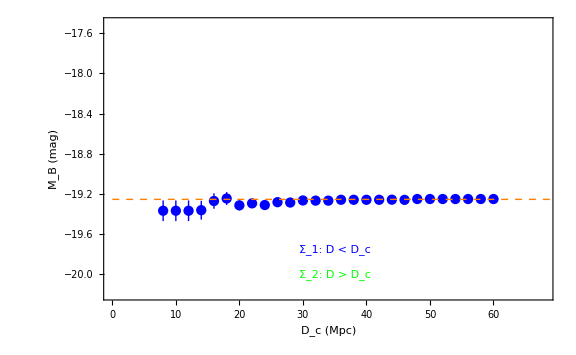
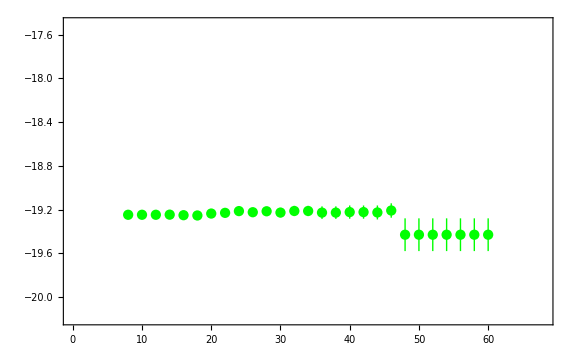
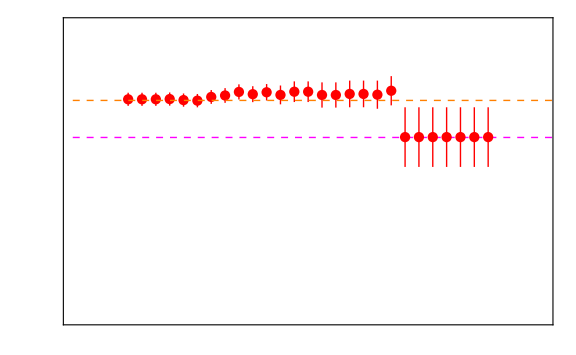

```mathematica
plh0dat={};
plparsdat={};
plparldat={};
plsdist={};
plchi2min={};
plchi2red={};
plaic={};
pldaic={};
plbic={};
pldbic={};
Do[
percol1s=percol1;
percol1l=percol1;
Do[
If[dist1[[i]]≥ dcrit,percol1s[[i]]=0]; (* in the nearby Subscript[M, B,s] column put 0 in the distant elements ie those that are beyond dcrit *)
If[0<=dist1[[i]]< dcrit,percol1l[[i]]=0] (* in the distant Subscript[M, B,l] column put 0 in the nearby elements ie those that are closer than dcrit. Elements with negative distance are ignored. *)
,{i,1,Length[dist1]}];
trL1=Drop[trL,{col}] ;(* Remove the MB column of L to replace it with two other columns for the nearby and distant parameters (Subscript[M, B,s] and Subscript[M, B,l]) *)
trL2=Insert[Insert[trL1,percol1s,col],percol1l,col+1] ;(* Replace with the new columns *)
Lnew=Transpose[trL2]; (* this is the model matrix Lnew for the new model with one new parameter *)
trLnew=trL2 ;(* The system is Y=L qpar. qpar has single column with 47 entries. Entry 45 is useless and does not appear anywhere but we keep it for completeness as it has been included in the fits data but it is not mentioned in Riess 21. *);
sigma=Inverse[trLnew.InvCall.Lnew];
qbf=sigma.(trLnew.InvCall.Y) ;(* These are the best fit parameter values. These formulas are proven in https://people.duke.edu/~hpgavin/SystemID/CourseNotes/linear-least-squres.pdf eq. 11 *);
(* the best fit papameter values with 1 sigma errors for H0 and for the two new parameters *)
h0=10^(qbf[[48]]/5) (* We obtain the correct value of h0 since qbf[[47]]= 5 log Subscript[H, 0] *);
dqbf48=Sqrt[sigma[[48,48]]];
dh0=Log[10] h0 dqbf48/5 ;
vec=Y-Lnew.qbf;
chi2min=vec.InvCall.vec;
Print["Distance=",dcrit,"---------------"];
Print["H_0=",h0,"±",dh0];
dpars=Sqrt[sigma[[col,col]]];
dparl=Sqrt[sigma[[col+1,col+1]]];
pars=ToString[qpar1[[col]]];
parl=ToString[qpar1[[col+1]]];
sdist=Abs[(qbf[[col]] -qbf[[col+1]])]/(dpars ^2+dparl ^2)^0.5 (* We obtain the σ-distance *);
Print[pars,"=",qbf[[col]],"±",dpars];
Print[parl,"=",qbf[[col+1]],"±",dparl];
Print["σ-distance = ",sdist];
Print["Mw","=",qbf[[39]],"±",Sqrt[sigma[[39,39]]]];
Print["Δbw","=",qbf[[42]],"±",Sqrt[sigma[[42,42]]]];
Print["Zw","=",qbf[[45]],"±",Sqrt[sigma[[45,45]]]];
Print["χ_min^2 = ",chi2min];
Print["χ_red^2 = ",chi2min/dof];
Print["AIC = ",chi2min+2*MM];
Print["ΔAIC = ",chi2min+2*MM-3646.7593303](* this is the AIC obtained from the zero order model of SHOES (see Baseline1 file)*);
Print["BIC = ",chi2min+MM*Log[NN]];
Print["ΔBIC = ",chi2min+MM*Log[NN]-3936.1961364](* this is the BIC obtained from the zero order model of SHOES (see Baseline1 file)*);
AppendTo[plh0dat,{dcrit,Around[h0,dh0]}];
AppendTo[plparsdat,{dcrit,Around[qbf[[col]],dpars]}];
AppendTo[plparldat,{dcrit,Around[qbf[[col+1]],dparl]}];
AppendTo[plsdist,{dcrit,sdist}];
AppendTo[plchi2min,{dcrit,chi2min}];
AppendTo[plchi2red,{dcrit,chi2min/dof}];
AppendTo[plaic,{dcrit,chi2min+2*MM}];
AppendTo[pldaic,{dcrit,chi2min+2*MM-3646.7593303}](* this is the AIC obtained from the zero order model of SHOES (see Baseline1 file)*);
AppendTo[plbic,{dcrit,chi2min+MM*Log[NN]}];
AppendTo[pldbic,{dcrit,chi2min+MM*Log[NN]-3936.1961364}](* this is the BIC obtained from the zero order model of SHOES (see Baseline1 file)*);
chi2min0=3552.76 (* this is the Subscript[χ, min]^2 obtained from the zero order model of SHOES (see Baseline1 file)*);
deltachi2min=chi2min-chi2min0  (* this is the improvement of chi2min obtained by the introduction of the new parameter *),{dcrit,mindist,maxdist,step}]
data1=plparsdat;
data2=plparldat;
data3=plh0dat;
plot1=ListPlot[data1,PlotRange->{{0,maxdist+8},{-20.2,-17.5}},PlotStyle->Blue,ImagePadding->70,Frame->{{True,False},{True,True}},FrameStyle->Directive[{{Blue,Automatic},{Blue,Blue}},Thick],FrameLabel->{"D_c (Mpc)","M_B (mag)"},BaseStyle->{Large,FontFamily->"Times",18},Epilog->{{Dashing[{Small,Small}],Thickness[Medium],Orange,Line[{{0,-19.253},{90,-19.253}}]},{Blue,Inset["Σ_1: D < D_c",{35,-19.75}]},{Green,Inset["Σ_2: D > D_c",{35,-20}]}}];
plot2=ListPlot[data2,PlotRange->{{0,maxdist+8},{-20.2,-17.5}},PlotStyle->Green,ImagePadding->70,Frame->{{True,False},{True,True}},FrameStyle->Directive[{{Blue,Automatic},{Blue,Blue}},Thick],BaseStyle->{Large,FontFamily->"Times",18}];
plot3=ListPlot[data3,PlotRange->{{0,maxdist+8},{39,85}},PlotStyle->Red,ImagePadding->70,Axes->False,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},Thick],FrameLabel->{{None,"H_0 (km sec^-1 Mpc^-1)"},{None,None}},BaseStyle->{Large,FontFamily->"Times",18},Epilog->{{Dashing[{Small,Small}],Thickness[Medium],Orange,Line[{{0,73.04},{70,73.04}}]},{Dashing[{Small,Small}],Thickness[Medium],Magenta,Line[{{0,67.27},{70,67.27}}]}}];
figmb=Overlay[Show[#,ImageSize->Large]&/@{plot1,plot2,plot3}]
```

```mathematica
Export[NotebookDirectory[]<>"figmb.pdf",figmb,ImageResolution->1000];
```

## Figures 10, 11 (Cyan curves)

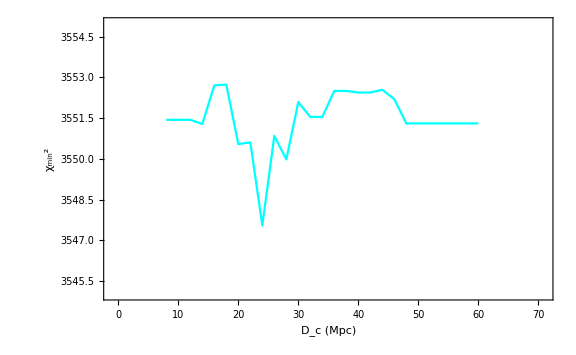

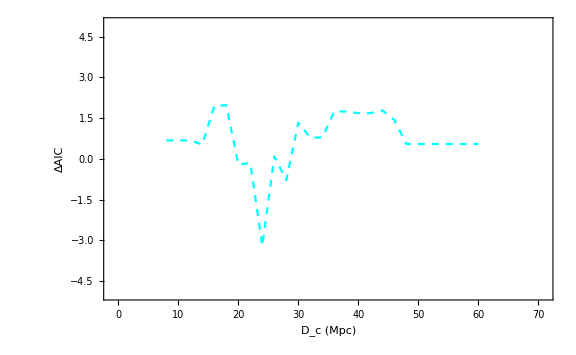

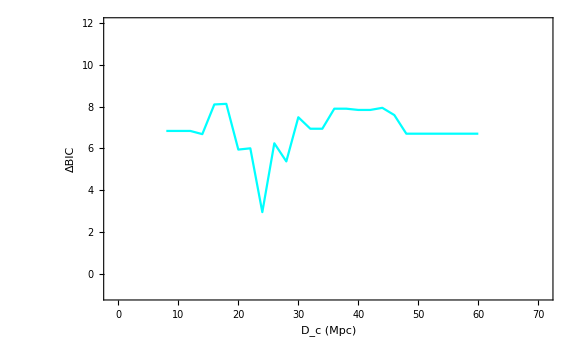

```mathematica
figsdmb=ListPlot[plsdist,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance (M_B)"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-0.5,4}},Axes->False,PlotStyle->{Cyan},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the σ-distance  plot obtained from the transition model Subscript[M, B] *);
figchimb=ListPlot[plchi2min,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_min^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3545,3555}},Axes->False,PlotStyle->{Cyan},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the Subscript[χ, min]^2  plot obtained from the transition model Subscript[M, B] *)
figchiredmb=ListPlot[plchi2red,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_red^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{1.0285,1.032}},Axes->False,PlotStyle->{Cyan},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the Subscript[χ, red]^2  plot obtained from the transition model Subscript[M, B] *);
figaicmb=ListPlot[plaic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","AIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3642,3651}},Axes->False,PlotStyle->{Cyan},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the AIC  plot obtained from the transition model Subscript[M, B] *);
figdaicmb=ListPlot[pldaic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔAIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-5,5}},Axes->False,PlotStyle->{Dashed,Cyan},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the ΔAIC  plot obtained from the transition model Subscript[M, B] *)
figbicmb=ListPlot[plbic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","BIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3938,3951}},Axes->False,PlotStyle->{Cyan},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the BIC  plot obtained from the transition model Subscript[M, B] *);
figdbicmb=ListPlot[pldbic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔBIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-1,12}},Axes->False,PlotStyle->{Cyan},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the ΔBIC  plot obtained from the transition model Subscript[M, B] *)
```